units
P->[Debye]/V[nm]^3=(0.021 M_i[e nm])/V[nm^3]=(0.021 M_i->Data)/(V->117.649)[e/nm^2]=0.00018*M_i->Data [e/nm^2]
P_lnr->[Debye]/V[nm]^3+(E/(k_B T V)[Debye])^2=0.00018*M_i->Data [e/nm^2]+[V/nm]/(1.38*10^-23[J/K]*298[K]*(117.649[nm])^3)((0.021)^2[e nm])^2*E*DATA=0.00018*M_i->Data [e/nm^2]+[V]/(48382*10^-23*([J][nm])^2)(0.021)^2[e^2]*E*DATA=0.00018*M_i->Data [e/nm^2]+[V]/(48382*10^-23*([V][C][nm])^2)(0.021)^2[e^2]*E*DATA=0.00018*M_i->Data [e/nm^2]+1/(48382*10^-23*([C][nm])^2)(0.021)^2[e^2]*E*DATA=0.00018*M_i->Data [e/nm^2]+1/(48382*10^-23*1/1.602(10^19[e][nm])^2)((0.021)^2[e])^2*E*DATA=0.00018*M_i->Data [e/nm^2]+(0.021)^2/(30201*10^-4*[nm]^2)[e]*E*DATA=0.00018*M_i->Data [e/nm^2]+0.00015[e/nm^2]*E*DATA

```mathematica
data=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.0-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mtotzerox=data[[All,2]]*0.00018;
mtotzeroy=data[[All,3]]*0.00018;
mtotzeroz=data[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtotzerox.dat",mtotzerox];
(*Export[NotebookDirectory[]<>"mtotzeroy.dat",mtotzeroy];
Export[NotebookDirectory[]<>"mtotzeroz.dat",mtotzeroz];*)
```

```mathematica
data01=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.1-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mtot01x=data01[[All,2]]*0.00018;
mtot01y=data01[[All,3]]*0.00018;
mtot01z=data01[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot01x.dat",mtot01x];
(*Export[NotebookDirectory[]<>"mtot01y.dat",mtot01y];
Export[NotebookDirectory[]<>"mtot01z.dat",mtot01z];*)
```

```mathematica
data02=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.2-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mtot02x=data02[[All,2]]*0.00018;
mtot02y=data02[[All,3]]*0.00018;
mtot02z=data02[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot02x.dat",mtot02x];
Export[NotebookDirectory[]<>"mtot02y.dat",mtot02y];
Export[NotebookDirectory[]<>"mtot02z.dat",mtot02z];
```

```mathematica
data03=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.3-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mtot03x=data03[[All,2]]*0.00018;
mtot03y=data03[[All,3]]*0.00018;
mtot03z=data03[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot03x.dat",mtot03x];
Export[NotebookDirectory[]<>"mtot03y.dat",mtot03y];
Export[NotebookDirectory[]<>"mtot03z.dat",mtot03z];
```

```mathematica
data04=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.4-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mtot04x=data04[[All,2]]*0.00018;
mtot04y=data04[[All,3]]*0.00018;
mtot04z=data04[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot04x.dat",mtot04x];
Export[NotebookDirectory[]<>"mtot04y.dat",mtot04y];
Export[NotebookDirectory[]<>"mtot04z.dat",mtot04z];
```

```mathematica
data05=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.5-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mtot05x=data05[[All,2]]*0.00018;
mtot05y=data05[[All,3]]*0.00018;
mtot05z=data05[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot05x.dat",mtot05x];
Export[NotebookDirectory[]<>"mtot05y.dat",mtot05y];
Export[NotebookDirectory[]<>"mtot05z.dat",mtot05z];
```

```mathematica
data06=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.6-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mtot06x=data06[[All,2]]*0.00018;
mtot06y=data06[[All,3]]*0.00018;
mtot06z=data06[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot06x.dat",mtot06x];
Export[NotebookDirectory[]<>"mtot06y.dat",mtot06y];
Export[NotebookDirectory[]<>"mtot06z.dat",mtot06z];
```

```mathematica
data07=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.7-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mtot07x=data07[[All,2]]*0.00018;
mtot07y=data07[[All,3]]*0.00018;
mtot07z=data07[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot07x.dat",mtot07x];
Export[NotebookDirectory[]<>"mtot07y.dat",mtot07y];
Export[NotebookDirectory[]<>"mtot07z.dat",mtot07z];
```

```mathematica
data08=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.8-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mtot08x=data08[[All,2]]*0.00018;
mtot08y=data08[[All,3]]*0.00018;
mtot08z=data08[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot08x.dat",mtot08x];
(*Export[NotebookDirectory[]<>"mtot08y.dat",mtot08y];
Export[NotebookDirectory[]<>"mtot08z.dat",mtot08z];*)
```

```mathematica
data1e2=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-2-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mtot1e2x=data1e2[[All,2]]*0.00018;
mtot1e2y=data1e2[[All,3]]*0.00018;
mtot1e2z=data1e2[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot1e2x.dat",mtot1e2x];
Export[NotebookDirectory[]<>"mtot1e2y.dat",mtot1e2y];
Export[NotebookDirectory[]<>"mtot1e2z.dat",mtot1e2z];
```

```mathematica
data1e3=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-3-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mtot1e3x=data1e3[[All,2]]*0.00018;
mtot1e3y=data1e3[[All,3]]*0.00018;
mtot1e3z=data1e3[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot1e3x.dat",mtot1e3x];
Export[NotebookDirectory[]<>"mtot1e3y.dat",mtot1e3y];
Export[NotebookDirectory[]<>"mtot1e3z.dat",mtot1e3z];
```

```mathematica
data1e4=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-4-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mtot1e4x=data1e4[[All,2]]*0.00018;
mtot1e4y=data1e4[[All,3]]*0.00018;
mtot1e4z=data1e4[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot1e4x.dat",mtot1e4x];
Export[NotebookDirectory[]<>"mtot1e4y.dat",mtot1e4y];
Export[NotebookDirectory[]<>"mtot1e4z.dat",mtot1e4z];
```

```mathematica
data1e5=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-5-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mtot1e5x=data1e5[[All,2]]*0.00018;
mtot1e5y=data1e5[[All,3]]*0.00018;
mtot1e5z=data1e5[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot1e5x.dat",mtot1e5x];
Export[NotebookDirectory[]<>"mtot1e5y.dat",mtot1e5y];
Export[NotebookDirectory[]<>"mtot1e5z.dat",mtot1e5z];
```

```mathematica
data1e6=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-6-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mtot1e6x=data1e6[[All,2]]*0.00018;
mtot1e6y=data1e6[[All,3]]*0.00018;
mtot1e6z=data1e6[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot1e6x.dat",mtot1e6x];
Export[NotebookDirectory[]<>"mtot1e6y.dat",mtot1e6y];
Export[NotebookDirectory[]<>"mtot1e6z.dat",mtot1e6z];
```

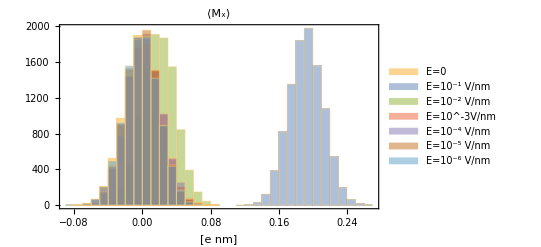

```mathematica
Histogram[{mtotzerox,mtot01x,mtot1e2x,mtot1e3x,mtot1e4x,mtot1e5x,mtot1e6x},PlotRange->All,Frame->True,ChartLegends->{"E=0","E=10^-1 V/nm","E=10^-2 V/nm","E=10^-3V/nm","E=10^-4 V/nm","E=10^-5 V/nm","E=10^-6 V/nm"},FrameLabel->{"[e nm]"},PlotLabel->"⟨M_x⟩"]
```

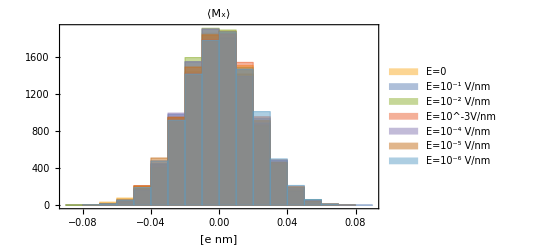

```mathematica
Histogram[{mtotzeroy,mtot01y,mtot1e2y,mtot1e3y,mtot1e4y,mtot1e5y,mtot1e6y},PlotRange->All,Frame->True,ChartLegends->{"E=0","E=10^-1 V/nm","E=10^-2 V/nm","E=10^-3V/nm","E=10^-4 V/nm","E=10^-5 V/nm","E=10^-6 V/nm"},FrameLabel->{"[e nm]"},PlotLabel->"⟨M_x⟩"]
```

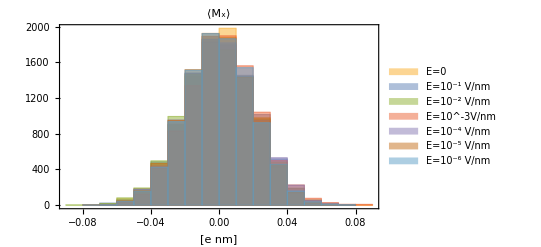

```mathematica
Histogram[{mtotzeroz,mtot01z,mtot1e2z,mtot1e3z,mtot1e4z,mtot1e5z,mtot1e6z},PlotRange->All,Frame->True,ChartLegends->{"E=0","E=10^-1 V/nm","E=10^-2 V/nm","E=10^-3V/nm","E=10^-4 V/nm","E=10^-5 V/nm","E=10^-6 V/nm"},FrameLabel->{"[e nm]"},PlotLabel->"⟨M_x⟩"]
```

```mathematica
datazerofull=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.0-V_nm/dipoles/Mtot_25ns_syst.xvg","Table"]//Drop[#,27]&;
mtotzerox=datazerofull[[All,2]]*0.00018;
mtotzeroy=datazerofull[[All,3]]*0.00018;
mtotzeroz=datazerofull[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtotxzerofull.dat",mtotzerox];
Export[NotebookDirectory[]<>"mtotyzerofull.dat",mtotzeroy];
Export[NotebookDirectory[]<>"mtotzzerofull.dat",mtotzeroz];
```

```mathematica
data1e2full=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-2-V_nm/dipoles/Mtot_25ns_syst.xvg","Table"]//Drop[#,27]&;
mtot1e2x=data1e2full[[All,2]]*0.00018;
mtot1e2y=data1e2full[[All,3]]*0.00018;
mtot1e2z=data1e2full[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtotx1e2full.dat",mtot1e2x];
Export[NotebookDirectory[]<>"mtoty1e2full.dat",mtot1e2y];
Export[NotebookDirectory[]<>"mtotz1e2full.dat",mtot1e2z];
```

```mathematica
data1e3full=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-3-V_nm/dipoles/Mtot_25ns_syst.xvg","Table"]//Drop[#,27]&;
mtot1e3x=data1e3full[[All,2]]*0.00018;
mtot1e3y=data1e3full[[All,3]]*0.00018;
mtot1e3z=data1e3full[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtotx1e3full.dat",mtot1e3x];
Export[NotebookDirectory[]<>"mtoty1e3full.dat",mtot1e3y];
Export[NotebookDirectory[]<>"mtotz1e3full.dat",mtot1e3z];
```

```mathematica
data1e4full=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-4-V_nm/dipoles/Mtot_25ns_syst.xvg","Table"]//Drop[#,27]&;
mtot1e4x=data1e4full[[All,2]]*0.00018;
mtot1e4y=data1e4full[[All,3]]*0.00018;
mtot1e4z=data1e4full[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtotx1e4full.dat",mtot1e4x];
Export[NotebookDirectory[]<>"mtoty1e4full.dat",mtot1e4y];
Export[NotebookDirectory[]<>"mtotz1e4full.dat",mtot1e4z];
```

```mathematica
data1e5full=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-5-V_nm/dipoles/Mtot_25ns_syst.xvg","Table"]//Drop[#,27]&;
mtot1e5x=data1e5full[[All,2]]*0.00018;
mtot1e5y=data1e5full[[All,3]]*0.00018;
mtot1e5z=data1e5full[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtotx1e5full.dat",mtot1e5x];
Export[NotebookDirectory[]<>"mtoty1e5full.dat",mtot1e5y];
Export[NotebookDirectory[]<>"mtotz1e5full.dat",mtot1e5z];
```

```mathematica
data1e6full=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-6-V_nm/dipoles/Mtot_25ns_syst.xvg","Table"]//Drop[#,27]&;
mtot1e6x=data1e6full[[All,2]]*0.00018;
mtot1e6y=data1e6full[[All,3]]*0.00018;
mtot1e6z=data1e6full[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtotx1e6full.dat",mtot1e6x];
Export[NotebookDirectory[]<>"mtoty1e6full.dat",mtot1e6y];
Export[NotebookDirectory[]<>"mtotz1e6full.dat",mtot1e6z];
```

```mathematica
data01full=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.1-V_nm/dipoles/Mtot_25ns_syst.xvg","Table"]//Drop[#,27]&;
mtot01x=data01full[[All,2]]*0.00018;
mtot01y=data01full[[All,3]]*0.00018;
mtot01z=data01full[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot01xfull.dat",mtot01x];
Export[NotebookDirectory[]<>"mtot01yfull.dat",mtot01y];
Export[NotebookDirectory[]<>"mtot01zfull.dat",mtot01z];
```

```mathematica
data02full=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.2-V_nm/dipoles/Mtot_25ns_syst.xvg","Table"]//Drop[#,27]&;
mtot02x=data02full[[All,2]]*0.00018;
mtot02y=data02full[[All,3]]*0.00018;
mtot02z=data02full[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot02xfull.dat",mtot02x];
Export[NotebookDirectory[]<>"mtot02yfull.dat",mtot02y];
Export[NotebookDirectory[]<>"mtot02zfull.dat",mtot02z];
```

```mathematica
data03full=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.3-V_nm/dipoles/Mtot_25ns_syst.xvg","Table"]//Drop[#,27]&;
mtot03x=data03full[[All,2]]*0.00018;
mtot03y=data03full[[All,3]]*0.00018;
mtot03z=data03full[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot03xfull.dat",mtot03x];
Export[NotebookDirectory[]<>"mtot03yfull.dat",mtot03y];
Export[NotebookDirectory[]<>"mtot03zfull.dat",mtot03z];
```

```mathematica
data04full=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.4-V_nm/dipoles/Mtot_25ns_syst.xvg","Table"]//Drop[#,27]&;
mtot04x=data04full[[All,2]]*0.00018;
mtot04y=data04full[[All,3]]*0.00018;
mtot04z=data04full[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot04xfull.dat",mtot04x];
Export[NotebookDirectory[]<>"mtot04yfull.dat",mtot04y];
Export[NotebookDirectory[]<>"mtot04zfull.dat",mtot04z];
```

```mathematica
data05full=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.5-V_nm/dipoles/Mtot_25ns_syst.xvg","Table"]//Drop[#,27]&;
mtot05x=data05full[[All,2]]*0.00018;
mtot05y=data05full[[All,3]]*0.00018;
mtot05z=data05full[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot05xfull.dat",mtot05x];
Export[NotebookDirectory[]<>"mtot05yfull.dat",mtot05y];
Export[NotebookDirectory[]<>"mtot05zfull.dat",mtot05z];
```

```mathematica
data06full=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.6-V_nm/dipoles/Mtot_25ns_syst.xvg","Table"]//Drop[#,27]&;
mtot06x=data06full[[All,2]]*0.00018;
mtot06y=data06full[[All,3]]*0.00018;
mtot06z=data06full[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot06xfull.dat",mtot06x];
Export[NotebookDirectory[]<>"mtot06yfull.dat",mtot06y];
Export[NotebookDirectory[]<>"mtot06zfull.dat",mtot06z];
```

```mathematica
data07full=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.7-V_nm/dipoles/Mtot_25ns_syst.xvg","Table"]//Drop[#,27]&;
mtot07x=data07full[[All,2]]*0.00018;
mtot07y=data07full[[All,3]]*0.00018;
mtot07z=data07full[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot07xfull.dat",mtot07x];
Export[NotebookDirectory[]<>"mtot07yfull.dat",mtot07y];
Export[NotebookDirectory[]<>"mtot07zfull.dat",mtot07z];
```

```mathematica
data08full=Import["/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.8-V_nm/dipoles/Mtot_25ns_syst.xvg","Table"]//Drop[#,27]&;
mtot08x=data08full[[All,2]]*0.00018;
mtot08y=data08full[[All,3]]*0.00018;
mtot08z=data08full[[All,4]]*0.00018;
Export[NotebookDirectory[]<>"mtot08xfull.dat",mtot08x];
Export[NotebookDirectory[]<>"mtot08yfull.dat",mtot08y];
Export[NotebookDirectory[]<>"mtot08zfull.dat",mtot08z];
```